x = 1.03261 ± 0.0612596

Δ = -60.4275° ± 9.35001°

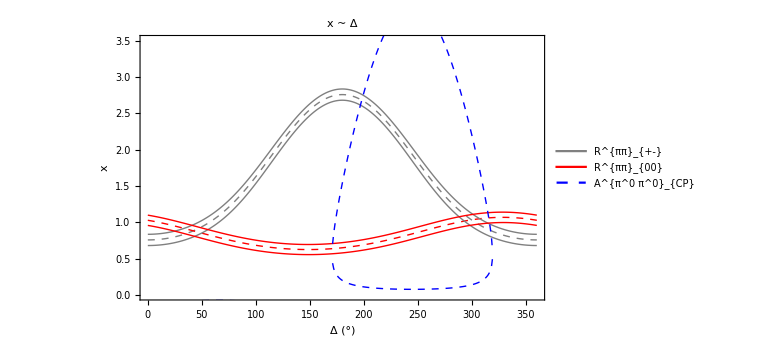

```mathematica
ClearAll["Global`*"];

nbDir=NotebookDirectory[];
projectDir=ParentDirectory[nbDir];

Get[FileNameJoin[{projectDir,"src","init.wl"}]];

{R000,R00Err}=Import[FileNameJoin[{projectDir,"results","B_pipi_R00_Rpm","R00.mx"}]];
{Rpm0,RpmErr}=Import[FileNameJoin[{projectDir,"results","B_pipi_R00_Rpm","Rpm.mx"}]];

inputs=<|
"A"->Acppippim0,
"S"->Scppippim0,
"gamma"->gamma0,
"phid"->phid0,
"Rpm"->Rpm0,
"R00"->R000,
"Acp00"->Acppi0pi00
|>;

paramSpecs={
{"A",Acppippim0,AcppippimErr},
{"S",Scppippim0,ScppippimErr},
{"gamma",gamma0,gammaErr},
{"phid",phid0,phidErr},
{"Rpm",Rpm0,RpmErr},
{"R00",R000,R00Err}
};

centerRes=ComputeXDeltaCenter[inputs,"DeltaStepDeg"->1];

compute=Function[in,ComputeXDeltaCenter[in,"DeltaStepDeg"->1]];
scalarExtractor=Function[res,res["Center"]];
curveExtractor=Function[res,res["Curves"]];

uncRes=ComputeUncertaintyFD[compute,scalarExtractor,curveExtractor,inputs,paramSpecs];

x0=centerRes["Center"]["x"];
dx=uncRes["Scalars"]["Sigma"]["x"];

Delta0deg=centerRes["Center"]["Delta"]/Degree;
dDeltadeg=uncRes["Scalars"]["Sigma"]["Delta"]/Degree;

Print["x = ",x0," ± ",N[dx,3]];
Print["Δ = ",Delta0deg,"° ± ",N[dDeltadeg,3],"°"];

PlotXDelta[centerRes,uncRes]
```